вариант 8
Задание 1

1.+1.09861 x+0.603488 x^2+0.220996 x^3+0.0606295 x^4+0.0133283 x^5+0.00254916 x^6+0.000396293 x^7

3 Log[3]^8

1.23352×10^-6

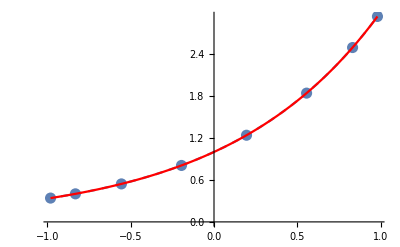

```mathematica
f[x_]=3^x;
a=-1;
b=1;
n=7;
Do[{Subscript[x, i]=Cos[(π(2*i+1))/(2(n+1))]//N,Subscript[f, i]=f[Subscript[x, i]]},{i,0,n}]
Do [Subscript[l, k][x_]=(∏_(i=0)^(k-1) (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^n (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i])), {k,0,n}]
P[x_]=∑_(k=0)^n Subscript[l, k][x] Subscript[f, k]//Expand
M1=Maximize[{D[f[x],{x,n+1}],a≤ x≤ b},x][[1]];
M2=Minimize[{D[f[x],{x,n+1}],a≤ x≤ b},x][[1]];
M=Max[Abs[M1],Abs[M2]]
R=M/(2^n*(n+1)!)//N
Tbl=Table[{Subscript[x, i], Subscript[f, i]},{i,0,n}];
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,-1,1},PlotStyle->Dashed];
Gr3=Plot[f[x], {x,Subscript[x, 0],Subscript[x, n]}, PlotStyle->Red];
Show [Gr1, Gr2, Gr3]
```

Задание 2

True

7

0.999999+0.0000316731 x-0.405228 x^2+0.000641159 x^3+0.0264275 x^4+0.00072653 x^5-0.00107556 x^6+0.000088014 x^7

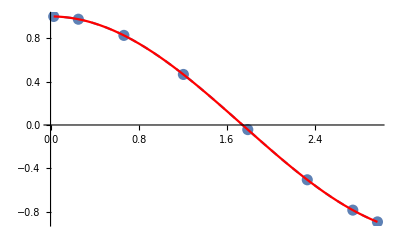

```mathematica
f[x_]=Cos[0.9 x];
a=0;
b=3;
ϵ=10^-5;
M1:=Maximize[{D[f[x],{x,n+1}],a≤ x≤ b},x][[1]];
M2:=Minimize[{D[f[x],{x,n+1}],a≤ x≤ b},x][[1]];
M:=Max[Abs[M1],Abs[M2]]
n=1;
While[(R=(M(b-a)^(n+1))/(2^(2n+1)(n+1)!))>ϵ,n++]
R<ϵ
n
Do[{Subscript[x, i]=(b-a)/2 Cos[(π(2*i+1))/(2(n+1))]+(a+b)/2//N,Subscript[f, i]=f[Subscript[x, i]]},{i,0,n}]
Do [Subscript[l, k][x_]=(∏_(i=0)^(k-1) (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^n (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i])), {k,0,n}];
P[x_]=∑_(k=0)^n Subscript[l, k][x] Subscript[f, k]//Expand
Tbl=Table[{Subscript[x, i], Subscript[f, i]},{i,0,n}];
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,a,b},PlotStyle->Dashed];
Gr3=Plot[f[x], {x,Subscript[x, 0],Subscript[x, n]}, PlotStyle->Red];
Show [Gr1, Gr2, Gr3]
```